# Areas and Volumes Assignment

### Instructions

Welcome to the assignment for Areas and Volumes. The purpose of this assignment is to assess your ability to plot areas and volumes. Some things to remember as you complete this assignment:
1. Save the notebook to your computer right away, and save your work often. 
2. When you have finished all the exercises, close any unnecessary cells and save as a PDF. (Make sure you Rasterize all 3-dimensional plots)
3. Upload the PDF on Canvas.
4. Do not delete this notebook. Save all your work until after the semester is over and your final grade has been issued.

Due Date:
see Canvas

### Question 1

a) Use RegionPlot to plot the 2-D region bounded above by the function y(x)=-x^2+2x+2 and bounded below by the x-axis. Let your plot window have an x and y range of -2 to 3.

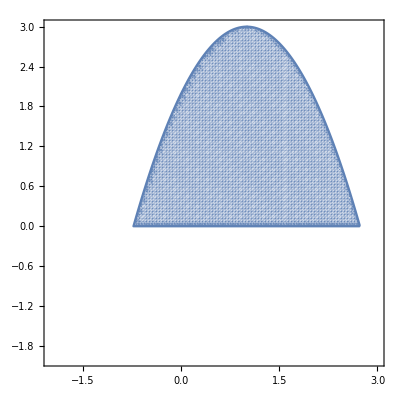

```mathematica
RegionPlot[0≤y≤-x^2+2x+2,{x,-2,3},{y,-2,3},PlotPoints->100]
```

b) Use RegionPlot to plot the 2-D region bounded above by y=-x^2+2x+2 and bounded below by y=1.5x.  Use the same plot window as in part a.

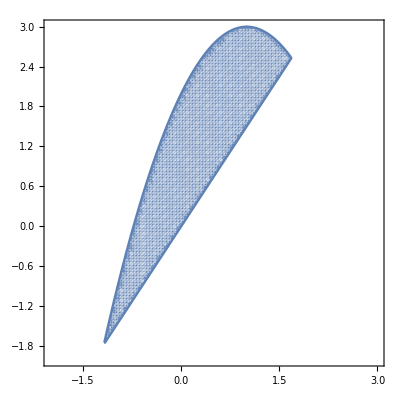

```mathematica
RegionPlot[1.5x≤y≤-x^2+2x+2,{x,-2,3},{y,-2,3},PlotPoints->100]
```

### Question 2

a) Use the Plot3D command to plot the surface z =2 y^3+2 x^3+2x y^2+16 . Display a plot with a range of x and y values from -2 to 10. (Reminder: don’t forget to rasterize your 3-D plot.)

```mathematica
Plot3D[2 y^3+2 x^3+2x y^2+16,{x,-2,10},{y,-2,10}]//Rasterize
```

-Graphics-

b) Use the RegionPlot3D command to create the volume below the surface and above the rectangular region in the xy-plane where x and y are bounded between 2 and 7. To better view your volume, let your plot window have an x and y range of 2 to 8 and let the z values be displayed from -10 to 1200. (Reminder: don’t forget to rasterize your 3-D plot.)

```mathematica
RegionPlot3D[0≤z≤2 y^3+2 x^3+2x y^2+16&&2<x≤7&&2<y≤7,{x,2,8},{y,2,8},{z,-10,1200},AxesLabel->{x,y,z},PlotPoints->100]//Rasterize
```

-Graphics-

c) Use the RegionPlot3D command to create the volume that is under the surface z =2 y^3+2 x^3+2x y^2+16 but above the region in the xy-plane described in Question 1 part “a”, that is, the 2-D region bounded between y=-x^2+x+2 and the x-axis. Use the viewing dimensions x and y from -2 to 3 and z from 0 to 50. The picture will be clearer if you add PlotPoints -> 100 in the RegionPlot3D command. (Reminder: don’t forget to rasterize your 3-D plot.)

```mathematica
RegionPlot3D[0≤z≤2 y^3+2 x^3+2x y^2+16&&-2<x<3&&0≤y≤-x^2+2x+2,{x,-2,3},{y,-2,3},{z,0,50},AxesLabel->{x,y,z},PlotPoints->100]//Rasterize
```

-Graphics-